# Time Series Summarization

Yun-chi Tang

Mentor: Dariia Porechna

Github: https://github.com/altan4377/WSS-2019

## Introduction

Abstract
Given a time series, find out the most efficient way to partition the time series into year, months, weeks, dates, etc. for faster calculations of maximum, minimum, and mean across the series. 
Description
Suppose one wants to know the average temperature throughout a time series. With the existing resources, the only option is to calculate the average of every single data point for the entire time interval. This option, however, is extremely inefficient as every point is needed in order to generate the average. To solve this problem, we examine how we may divide the time series into years, months, weeks, dates, and hours so that when the average is calculated, we can simply extract the temperature values for the years, months, etc. and reduce the number of objects that is needed for the average to be calculated. 
I will start by extracting the complete years that occur during this time series. By doing so, we created objects that will represent all the data points for that year. We may then continue this process and extract the complete months from the time that does not assemble a complete year. Then, we continue this process by grouping the dates that are left into combinations of six-day weeks and days.

## Time Series

In this section I am going to construct the most optimal way to express a time series as a combination of complete years, months, weeks, dates, and hours.

### Set Up

Find the year, month, date, and hour of the date object

```mathematica
findYear[date_DateObject] := Part[DateList[date],1]
```

```mathematica
findMonth[date_DateObject] := Part[DateList[date],2]
```

```mathematica
findDate[date_DateObject] := Part[DateList[date],3]
```

```mathematica
findHour[date_DateObject] := Part[DateList[date],4]
```

The “startDate” and the “endDate” generates the dates that the day-week-month-year optimization should begin based on if the first/last date is complete. Note that the examination of whether the first/last part is complete is a recurring theme throughout the set up and will be used every time to ensure complete objects are treated as complete objects instead of the sum of its parts.

```mathematica
startDate[start_DateObject] := If[findHour[start] == 0, start, start +Quantity[1,"Days"]]
```

```mathematica
endDate[end_DateObject] := If[findHour[end] == 23, end, end - Quantity[1,"Days"]]
```

A couple of set up functions: The first one deals with setting the number of days in the month. The next two deals with converting date object to string form (and we are going to let it be a listable function).

```mathematica
daysInMonth[date_DateObject] := If[Mod[findYear[date],4] == 0, Part[{31,29,31,30,31,30,31,31,30,31,30,31},findMonth[date]],Part[{31,28,31,30,31,30,31,31,30,31,30,31},findMonth[date]]]
```

```mathematica
convertDateToString[date_DateObject] := IntegerString[10000 * findYear[date] + 100 * findMonth[date] + findDate[date],10]
```

```mathematica
SetAttributes[convertDateToString,Listable]
```

Now we write the code to find the year, month, and date parts. 
First, years:

```mathematica
findCompleteYearsBetween[start_DateObject,end_DateObject] :=
ToString /@Select[Flatten[Table[m,{m,findYear[ startDate[start]],findYear[endDate[end]]}]],findYear[ startDate[start]]*10000+findMonth[ startDate[start]]*100+findDate[ startDate[start]]≤ #*10000+101 && #*10000+1200+daysInMonth[endDate[end]]≤ findYear[endDate[end]]*10000+findMonth[endDate[end]]*100+findDate[endDate[end]]&]
```

Then: months (for before a full year, after a full year, and between two days if the two dates do not cover the entire year:

```mathematica
findMonthsAfter[start_DateObject] := 
If[findMonth[start] == 1 && findDate[start] == 1 && findHour[start] == 0, {},
If[findDate[startDate[start]] == 1, Table[StringJoin[{IntegerString[findYear[startDate[start]],10,4],IntegerString[n,10,2]}], {n,findMonth[startDate[start]],12}], Table[StringJoin[{IntegerString[findYear[startDate[start]],10,4],IntegerString[n,10,2]}], {n,findMonth[startDate[start]]+1,12}]]]
```

```mathematica
findCompleteMonthsBetween[start_DateObject,end_DateObject] := ToString /@Select[Flatten[Table[100*m+n,{m,findYear[startDate[start]],findYear[end]},{n,1,12}]],findYear[startDate[start]]*10000+findMonth[startDate[start]]*100+findDate[startDate[start]]≤ #*100+1 && #*100+daysInMonth[endDate[end]]≤ findYear[endDate[end]]*10000+findMonth[endDate[end]]*100+findDate[endDate[end]]&]
```

```mathematica
findMonthsBefore[end_DateObject] := 
If[findMonth[end] == 12 && findDate[end] == 31 && findHour[end] == 23, {},
If[findDate[endDate[end]] == daysInMonth[endDate[end]],Table[StringJoin[{IntegerString[findYear[endDate[end]],10,4],IntegerString[n,10,2]}], {n,1,findMonth[endDate[end]]}],Table[StringJoin[{IntegerString[findYear[endDate[end]],10,4],IntegerString[n,10,2]}], {n,1,findMonth[endDate[end]]-1}]]]
```

Weeks and Dates. 
Throughout this process, I make a decision to group the dates into six-day weeks into the traditional seven-day format for two reasons: 
1) This will overall allow the spare parts to be more efficiently grouped as the possible number of days in months (28, 29, 30, 31), especially the latter two which will be used extremely often, will have a significantly smaller remainder when divided by 6 compared to when they are divided by 7. 
2) This will eliminate any potential for the need to reconsider the optimization strategy for the beginning and the ending of the time series: If the traditional seven-day week format is used, then the optimizing strategy will take one extra step because if we consider the time series [June 1st, July 5th], then grouping this time series into 5 weeks instead of the month of June plus 5 days will mean that less objects is needed when we calculate the average. Using the six-day week format will eliminate such concerns. Once we extracted the weeks and dates, we will create the most efficient combination for this time series.

```mathematica
listWeekDatesBegin[dateStart_DateObject] := If[findHour[dateStart]== 0,(ToString/@If[findDate[dateStart]== 1,{},Join[Select[Table[n,{n,findYear[dateStart]*10000+findMonth[dateStart]*100+findDate[dateStart],findYear[dateStart]*10000+findMonth[dateStart]*100+daysInMonth[dateStart]}],#-(findYear[dateStart]*10000+findMonth[dateStart]*100+findDate[dateStart])<  Mod[daysInMonth[dateStart]-findDate[dateStart]+1,6]&],Reverse[Table[StringJoin[{IntegerString[findYear[dateStart],10,4],IntegerString[findMonth[dateStart],10,2],IntegerString[n,10,2],"W"}],{n,daysInMonth[dateStart]-5,findDate[dateStart],-6}]]]]),
(ToString/@If[findDate[dateStart+ Quantity[1,"Days"]]== 1,{},Join[Select[Table[n,{n,findYear[dateStart+ Quantity[1,"Days"]]*10000+findMonth[dateStart+ Quantity[1,"Days"]]*100+findDate[dateStart+Quantity[1,"Days"]],findYear[dateStart+Quantity[1,"Days"]]*10000+findMonth[dateStart+ Quantity[1,"Days"]]*100+daysInMonth[dateStart+ Quantity[1,"Days"]]}],#-(findYear[dateStart+Quantity[1,"Days"]]*10000+findMonth[dateStart+ Quantity[1,"Days"]]*100+findDate[dateStart+Quantity[1,"Days"]])<  Mod[daysInMonth[dateStart+ Quantity[1,"Days"]]-findDate[dateStart+ Quantity[1,"Days"]]+1,6]&],Reverse[Table[StringJoin[{IntegerString[findYear[dateStart+ Quantity[1,"Days"]],10,4],IntegerString[findMonth[dateStart+ Quantity[1,"Days"]],10,2],IntegerString[n,10,2],"W"}],{n,daysInMonth[dateStart+ Quantity[1,"Days"]]-5,findDate[dateStart+ Quantity[1,"Days"]],-6}]]]])]
```

```mathematica
listWeekDatesEnd[dateEnd_DateObject] := 
If[findHour[dateEnd] == 23,(ToString/@ If[findDate[dateEnd] == daysInMonth[dateEnd],{},Join[Table[StringJoin[{IntegerString[findYear[dateEnd],10,4],IntegerString[findMonth[dateEnd],10,2],IntegerString[n,10,2],"W"}],{n,1,findDate[dateEnd]-5,6}],Select[Table[n,{n,findYear[dateEnd]*10000+findMonth[dateEnd]*100+1,findYear[dateEnd]*10000+findMonth[dateEnd]*100+findDate[dateEnd]}],(findYear[dateEnd]*10000+findMonth[dateEnd]*100+findDate[dateEnd])-#< Mod[findDate[dateEnd],6]&]]]),
(ToString/@ If[findDate[dateEnd-Quantity[1,"Days"]] == daysInMonth[dateEnd-Quantity[1,"Days"]],{},Join[Table[StringJoin[{IntegerString[findYear[dateEnd-Quantity[1,"Days"]],10,4],IntegerString[findMonth[dateEnd-Quantity[1,"Days"]],10,2],IntegerString[n,10,2],"W"}],{n,1,findDate[dateEnd-Quantity[1,"Days"]]-5,6}],Select[Table[n,{n,findYear[dateEnd-Quantity[1,"Days"]]*10000+findMonth[dateEnd-Quantity[1,"Days"]]*100+1,findYear[dateEnd-Quantity[1,"Days"]]*10000+findMonth[dateEnd-Quantity[1,"Days"]]*100+findDate[dateEnd-Quantity[1,"Days"]]}],(findYear[dateEnd-Quantity[1,"Days"]]*10000+findMonth[dateEnd-Quantity[1,"Days"]]*100+findDate[dateEnd-Quantity[1,"Days"]])-#< Mod[findDate[dateEnd-Quantity[1,"Days"]],6]&]]])]
```

Lastly, Hours:

```mathematica
findHourlySetsAfter[start_DateObject] := If[findHour[start] == 0, {}, Table[StringJoin[{IntegerString[findYear[start],10,4],IntegerString[findMonth[start],10,2],IntegerString[findDate[start],10,2],IntegerString[n,10,2]}],{n,findHour[start],23}]]
```

```mathematica
findHourlySetsBefore[end_DateObject] := 
If[findHour[end] == 23, {},
Table[StringJoin[{IntegerString[findYear[end],10,4],IntegerString[findMonth[end],10,2],IntegerString[findDate[end],10,2],IntegerString[n,10,2]}],{n,0,findHour[end]}]]
```

### Applying The Set-Up To Generate The Most Optimal Combination.

Essentially, the mechanism goes as the following: 
- If there are complete years in between, then we take the complete year, and then the months, weeks, days, hours (in that order) before and after it. 
- If not: 
	- First we need to find the combination that involves using all the possible whole months
	- Then we need to find the combination that involves using none of the whole months
	- If the number of complete months between two objects is greater than or equal to 2, then apply the combination that involves using all the possible months; if the number of complete months between two objects is 0, then apply the combination that involves using none of the possible months; if the number of complete months is 1 then we compare the two combinations and select the one with the lower number of objects.

```mathematica
combinationWithYear[start_DateObject, end_DateObject] := Join[findHourlySetsAfter[start],listWeekDatesBegin[start],findMonthsAfter[start],findCompleteYearsBetween[start,end],findMonthsBefore[end],listWeekDatesEnd[end],findHourlySetsBefore[end]]
```

```mathematica
combinationWithMonth[start_DateObject,end_DateObject] := 
Join[findHourlySetsAfter[start],listWeekDatesBegin[start],findCompleteMonthsBetween[start,end],listWeekDatesEnd[end],findHourlySetsBefore[end]]
```

```mathematica
combinationWithoutMonth[start_DateObject,end_DateObject] :=Join[findHourlySetsAfter[start],Table[ StringJoin[convertDateToString[n],"W"], {n, startDate[start], endDate[end] - Quantity[5,"Days"] , Quantity[6,"Days"]}], convertDateToString/@
Select[Table[n,{n,DateObject[{findYear[startDate[start]],findMonth[startDate[start]],findDate[startDate[start]]}],endDate[end],Quantity[1,"Days"]}],QuantityMagnitude[DateObject[{findYear[endDate[end]],findMonth[endDate[end]],findDate[endDate[end]]}]-#]+1 <= Mod[QuantityMagnitude[DateObject[{findYear[endDate[end]],findMonth[endDate[end]],findDate[endDate[end]]}]-DateObject[{findYear[startDate[start]],findMonth[startDate[start]],findDate[startDate[start]]}]]+1,6]&],findHourlySetsBefore[end]]
```

```mathematica
combinationTwoMonthsPlus[start_DateObject,end_DateObject] := combinationWithMonth[start,end]
```

```mathematica
combinationOneMth[start_DateObject,end_DateObject] := First[SortBy[{combinationWithMonth[start,end],CombinationWithoutMonth[start,end]},Length[#]&]]
```

```mathematica
combinationNoMths[start_DateObject,end_DateObject]:= combinationWithoutMonth[start,end]
```

This function will generate, with all the information and functions at the above, the most efficient time series breakdown.

```mathematica
TimeSeriesCombination[start_DateObject,end_DateObject] := 
If[Length[findCompleteYearsBetween[start,end]]≥ 1, 
combinationWithYear[start,end],
If[Length[findCompleteMonthsBetween[start,end]] ≥ 2, 
combinationTwoMonthsPlus[start,end],
If[Length[findCompleteMonthsBetween[start,end]]== 1,
combinationOneMth[start,end],
combinationNoMths[start,end]]]]
```

Here is an example of what a summarized time series will look like:

```mathematica
TimeSeriesCombination[DateObject[{2019,6,2,1}],DateObject[{2019,7,5,0}]]
```

{2019060201,2019060202,2019060203,2019060204,2019060205,2019060206,2019060207,2019060208,2019060209,2019060210,2019060211,2019060212,2019060213,2019060214,2019060215,2019060216,2019060217,2019060218,2019060219,2019060220,2019060221,2019060222,2019060223,20190603W,20190609W,20190615W,20190621W,20190627W,20190703,20190704,2019070500}

To make this time series more readable, we can go ahead and group it by the type of object. In this case, all consecutive hours will be grouped together, than days, weeks, etc.

```mathematica
Column[SplitBy[TimeSeriesCombination[DateObject[{2017,6,2,15}],DateObject[{2019,7,12,0}]],StringLength[#]&]]
```

{2017060215,2017060216,2017060217,2017060218,2017060219,2017060220,2017060221,2017060222,2017060223}
{20170603,20170604,20170605,20170606}
{20170607W,20170613W,20170619W,20170625W}
{201707,201708,201709,201710,201711,201712}
{2018}
{201901,201902,201903,201904,201905,201906}
{20190701W}
{20190707,20190708,20190709,20190710,20190711}
{2019071200}

## Evaluation: Using Time Series To Calculate Weather Data

Using this optimized time series summarization, I can find the maximum, minimum, and the mean air temperature for a time series. For now, the functions only apply to Waltham, MA. An extra parameter will be needed to allow users to select their locations.

```mathematica
MaxTemperatureInterval[DateObject[{2016,8,13,0}],DateObject[{2018,2,23,23}]]
```

81.788 °F

```mathematica
MinTemperatureInterval[DateObject[{2016,8,13,0}],DateObject[{2018,2,23,23}]]
```

0.710001 °F

```mathematica
MeanTemperatureInterval[DateObject[{2016,8,13,0}],DateObject[{2018,2,23,23}]]
```

48.5953 °F

## Evaluation: How Efficient Is This Function?

We decided to conduct a test. We determine how time it takes for the algorithm we determined, and also the existing algorithm, to determine the mean temperature throughout 300 time series, each ending at 2018/12/31 but have lengths of 1 day, 2 days, ...  We find that initially the existing method is more efficient. However, as the number of days increase my method starts to prevail.

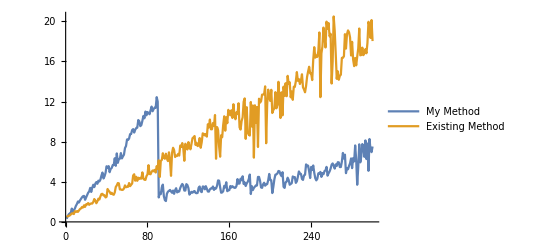

```mathematica
ListLinePlot[{Legended[Table[Part[Timing[Quantity[MeanTemperatureInterval[DateObject[{2018,12,31}]-Quantity[n,"Days"],DateObject[{2018,12,31}]],"DegreesFahrenheit"]],1],{n,300}],"My Method"],Legended[Table[Part[Timing[Mean[AirTemperatureData[LinguisticAssistant,{DateObject[{2018,12,31}]-Quantity[n,"Days"],DateObject[{2018,12,31}]}]]],1],{n,300}],"Existing Method"]}]
```

## Why This Function Is Actually More Important Than Just The Efficiency

To double check that my code makes sense, I go back to check the calculated value against the value that is calculated using the existing method. When I look at the values, there seems to be some differences.

```mathematica
Timing[Quantity[MeanTemperatureInterval[LinguisticAssistant,LinguisticAssistant],"DegreesFahrenheit"]]
```

{2.45313,52.1636 °F}

```mathematica
Timing[Mean[AirTemperatureData[LinguisticAssistant,{DateObject[{2016,2,3}],DateObject[{2018,11,16}]}]]]
```

{66.4063,52.0954 °F}

The difference is even bigger (up to 1.5 degrees Fahrenheit) when we are looking at smaller time intervals.

```mathematica
Timing[Quantity[MeanTemperatureInterval[LinguisticAssistant,LinguisticAssistant],"DegreesFahrenheit"]]
```

{0.390625,35.5266 °F}

```mathematica
Timing[Mean[AirTemperatureData[LinguisticAssistant,{DateObject[{2018,11,13}],DateObject[{2018,11,16}]}]]]
```

{0.3125,37.1745 °F}

While I wonder what is causing this difference, I remembered my initial experiment on time series and remembered that the number of data points for each day is not equal:

```mathematica
AirTemperatureData[LinguisticAssistant,{DateObject[{2018,11,13}],DateObject[{2018,11,14}]}]
```

TimeSeries[…]

```mathematica
AirTemperatureData[LinguisticAssistant,{DateObject[{2018,11,14}],DateObject[{2018,11,15}]}]
```

TimeSeries[…]

```mathematica
AirTemperatureData[LinguisticAssistant,{DateObject[{2018,11,15}],DateObject[{2018,11,16}]}]
```

TimeSeries[…]

Using the dataset that I have, I calculated and confirmed that the existing system simply takes all the data points during that time interval and averages it out. What this means is that the mechanism will favour some mechanisms over the others. In the case between 2018/11/13 to 2018/11/15, the temperature is larger because the date, whose temperature is 46.5 F (higher than the other two dates) is favoured during the calculation. Thus, my method of calculation will provide a more calculation of the mean because every day will have the same weight during the calculation. 
Note that my mechanism is not perfect. This comes from the fact that the daily temperatures are calculated with the same method that caused the accuracies in the existing mechanism, and the unequal representation of hours is a glaring issue in calculating daily temperatures:

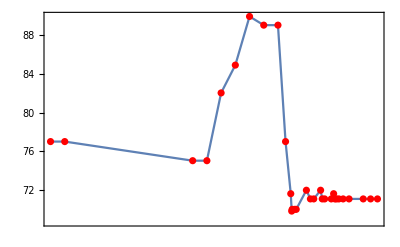

```mathematica
DateListPlot[AirTemperatureData[LinguisticAssistant,{DateObject[{2018,7,17}],DateObject[{2018,7,18}]}],Mesh -> All, MeshStyle -> Red]
```

In this case, the temperature during 2:00 and 10:00 is not even calculated! When calculating averages, 18:00-24:00 will be heavily favoured and the mean temperature for the date will be a lot close to the 70 F mark as a result. Thus, daily temperatures should eventually be calculated by averaging the values for all the hours.

## Using Time Series To Obtain Relevant Information About Weather Data

### Separate The Objects In The Combination Into Separate Lists

Recall the time series combination that we came up with in section 1? What we are going to do here is that we are going to go ahead and divide that giant list of representations into five categories: Complete years, months, weeks, dates, and hours. How we are going to do this is that we are going to examine the character of each object. Years will only have 4 digits, months will have two more (to denote the month), dates will have two more than that, weeks will have an extra “W” at the end whereas hours will have a two digit number at the end to denote the hour.

```mathematica
yearSet[start_DateObject,end_DateObject] := Select[TimeSeriesCombination[start,end],StringLength[#] == 4&];
```

```mathematica
monthSet[start_DateObject,end_DateObject] := Select[TimeSeriesCombination[start,end],StringLength[#] == 6&];
```

```mathematica
weekSet[start_DateObject,end_DateObject] :=Select[TimeSeriesCombination[start,end],StringLength[#] == 9&];
```

```mathematica
dateSet[start_DateObject,end_DateObject]:= Select[TimeSeriesCombination[start,end],StringLength[#] == 8&];
```

```mathematica
hourSet[start_DateObject,end_DateObject] := Select[TimeSeriesCombination[start,end],StringLength[#] == 10&];
```

Now, to grasp information on a particular year, month, etc., we need to get the data files first by getting the year number and importing the file that has information on all the (year or month or week or day or hour) information for that year.

```mathematica
temperatureFileYear[] := ToExpression @ First[Flatten[Import["all-years.csv"]]]
```

```mathematica
temperatureFileMonth[date_String] := ToExpression @ First[Flatten[Import[StringJoin[{StringTake[date,4],"-month.csv"}]]]]
```

```mathematica
temperatureFileWeek[date_String] := ToExpression @ First[Flatten[Import[StringJoin[{StringTake[date,4],"-week.csv"}]]]]
```

```mathematica
temperatureFileDay[date_String] := ToExpression @ First[Flatten[Import[StringJoin[{StringTake[date,4],"-day.csv"}]]]]
```

```mathematica
temperatureFileHour[date_String] := ToExpression @ First[Flatten[Import[StringJoin[{StringTake[date,4],"-hour.csv"}]]]]
```

Then we use the functions below to obtain information regarding the maximum, minimum, and mean value of the year, month, and week and the temperature of the day and hour.

```mathematica
temperatureYearMax[yearList_List] := temperatureFileYear[][#]["Max"]&/@yearList
```

```mathematica
temperatureYearMin[yearList_List] := temperatureFileYear[][#]["Min"]&/@yearList
```

```mathematica
temperatureYearMean[yearList_List] := temperatureFileYear[][#]["Mean"]&/@yearList
```

```mathematica
temperatureMonthMax[monthList_List] := temperatureFileMonth[#][#]["Max"]&/@monthList
```

```mathematica
temperatureMonthMin[monthList_List] := temperatureFileMonth[#][#]["Min"]&/@monthList
```

```mathematica
temperatureMonthMean[monthList_List] := temperatureFileMonth[#][#]["Mean"]&/@monthList
```

```mathematica
temperatureWeekMax[weekList_List] := temperatureFileWeek[#][#]["Max"]&/@weekList
```

```mathematica
temperatureWeekMin[weekList_List] := temperatureFileWeek[#][#]["Min"]&/@weekList
```

```mathematica
temperatureWeekMean[weekList_List] := temperatureFileWeek[#][#]["Mean"]&/@weekList
```

```mathematica
temperatureDay[dayList_List] := temperatureFileDay[#][#]["Temperature"]&/@dayList
```

```mathematica
temperatureHour[dayList_List] := temperatureFileHour[#][#]["Temperature"] &/@ dayList
```

Using that information, we are going to determine the maximum, minimum, and the mean temperature of whatever interval the function implementer requested. With maximum and minimum it is pretty straight forward because we can simply determine the max/min out of all of the values. However, with the mean temperature, we need to first determine how many days are in the year/month satisfied before we calculated average. This is because we need to keep in mind that the average for, let us say an entire year, represents the fact that when we calculate the average, we have to consider 365/366 days with the temperature at that number.

```mathematica
MaxTemperatureInterval[start_DateObject,end_DateObject] := Quantity[Max[Flatten[Join[temperatureYearMax[yearSet[start,end]],temperatureMonthMax[monthSet[start,end]],temperatureWeekMax[weekSet[start,end]],temperatureDay[dateSet[start,end]],temperatureHour[hourSet[start,end]]]]],"DegreesFahrenheit"]
```

```mathematica
MinTemperatureInterval[start_DateObject,end_DateObject] := Quantity[Min[Flatten[Join[temperatureYearMin[yearSet[start,end]],temperatureMonthMin[monthSet[start,end]],temperatureWeekMin[weekSet[start,end]],temperatureDay[dateSet[start,end]],temperatureHour[hourSet[start,end]]]]],"DegreesFahrenheit"]
```

```mathematica
daysInYear[year_Integer] := If[Mod[year,4]==0,366,365]
```

```mathematica
daysInMonth[month_Integer] := daysInMonth[DateObject[{(month - Mod[month,100])/100, Mod[month,100]}]]
```

```mathematica
MeanTemperatureInterval[start_DateObject,end_DateObject] := 
Quantity[(24*(Total[daysInYear @ Read[StringToStream[#],Number]&/@yearSet[start,end]*temperatureYearMean[yearSet[start,end]]]+
Total[daysInMonth @ Read[StringToStream[#],Number]&/@monthSet[start,end] * temperatureMonthMean[monthSet[start,end]]] + 
Total[(6*#)&/@temperatureWeekMean[weekSet[start,end]]] + Total[temperatureDay[dateSet[start,end]]])+Total[temperatureHour[hourSet[start,end]]])/
(QuantityMagnitude[DateObject[{findYear[end],findMonth[end],findDate[end],findHour[end]}]-DateObject[{findYear[start],findMonth[start],findDate[start],findHour[start]}]]+1),"DegreesFahrenheit"]
```

Let us put them to the test. Note these date objects are randomly selected.

## Data Pre-Computation

Please note that the data files are only for Waltham, MA for now. The goal eventually is to allow users to get data for more places.

To get data files, we need the directory first. (The data file producing process is intended to improve the Wolfram Knowledge Base)

```mathematica
SetDirectory["C:\\Users\\Albert\\Desktop\\Wolfram Summer School 2019\\Project\\Data Files"]
```

C:\Users\Albert\Desktop\Wolfram Summer School 2019\Project\Data Files

This section will concern with generating the database that will generate the weather temperature data in association form.

First we start with hours. However, it happens that there are certain hours with no data at all. This means that I will have to expand the time interval by an equal number of hours, one hour at a time, on each side to obtain the closest data point. We define a function first that may be expanded to other conditions (missing days, other location, etc.)

```mathematica
timeData[start_DateObject, end_DateObject, unit_Quantity, f_,location_] := If[Quiet[Check[f[location,{start,end}],Missing]=== Missing], timeData[start - 1 unit, end + 1 unit, unit,f],Mean[f[location,{start,end}]]]
```

With that, we generate the hourly data in association form.

```mathematica
hourlyData[year_Integer] := Monitor[<|Table[StringJoin[{IntegerString[year,10,4],IntegerString[month,10,2],IntegerString[date,10,2],IntegerString[hour,10,2]}]-> <|"Temperature" ->QuantityMagnitude[timeData[DateObject[{year,month,date,hour}],DateObject[{year,month,date,hour}]+Quantity[1,"hours"],Quantity[1,"hours"],AirTemperatureData,LinguisticAssistant]]|>,{month,12},{date,1,daysInMonth[DateObject[{year,month}]]},{hour,0,23}]|>,ProgressIndicator[month,{1,12}]]
```

Once we obtained the data, we generate the name of the file and export the data.

```mathematica
generateFileHour[yearNumber_Integer] := StringJoin[{IntegerString[yearNumber], "-hour.csv"}]
```

```mathematica
exportHourlyFile[year_Integer] := Export[generateFileHour[year],hourlyData[year]]
```

Next we find the daily data. We first find the daily temperature. (Note this is not as accurate as if it is calculated as the average of the hourly data. However, the efficiency may be similar due to the similar amount of data points)

```mathematica
dailyData[yearNumber_Integer] := 
<|Table[IntegerString[yearNumber * 10000+m*100+d]-> <|"Temperature" ->  QuantityMagnitude[Mean[AirTemperatureData[LinguisticAssistant,{DateObject[{yearNumber,m,d}],DateObject[{yearNumber,m,d}]+Quantity[1,"Days"]}]]]|> ,{m,1,12},{d,1,Part[Table[daysInMonth[DateObject[{yearNumber,k}]],{k,12}],m]}]
|>
```

Then we generate the file name of the data and export the data.

```mathematica
generateFileDay[yearNumber_Integer] := StringJoin[{IntegerString[yearNumber], "-day.csv"}]
```

```mathematica
exportDayFile[yearNumber_Integer] := Export[generateFileDay[yearNumber],dailyData[yearNumber]]
```

Now we move on to generate weekly data. Note that because it seems that it is more convenient to be able to have the week fall any time in the time series, we are generating data of all possible time series.

First, we import the daily data set.

```mathematica
dailyDataSet[yearNumber_Integer] := ToExpression@First[Flatten[Import[generateFileDay[yearNumber]]]]
```

The functions below will calculate the maximum, minimum, and mean air temperature for the week.

```mathematica
maxAirTemperatureWeek[startDate_DateObject] := Max[Table[dailyDataSet[findYear[startDate]][StringJoin[{IntegerString[findYear[startDate + Quantity[n,"Days"]],10,4],IntegerString[findMonth[startDate + Quantity[n,"Days"]],10,2],IntegerString[findDate[startDate + Quantity[n,"Days"]],10,2]}]]["Temperature"],{n,0,5}]]
```

```mathematica
minAirTemperatureWeek[startDate_DateObject] := Min[Table[dailyDataSet[findYear[startDate]][StringJoin[{IntegerString[findYear[startDate + Quantity[n,"Days"]],10,4],IntegerString[findMonth[startDate +Quantity[n,"Days"]],10,2],IntegerString[findDate[startDate +Quantity[n,"Days"]],10,2]}]]["Temperature"],{n,0,5}]]
```

```mathematica
meanAirTemperatureWeek[startDate_DateObject] :=Mean[Table[dailyDataSet[findYear[startDate]][StringJoin[{IntegerString[findYear[startDate +Quantity[n,"Days"]],10,4],IntegerString[findMonth[startDate + Quantity[n,"Days"]],10,2],IntegerString[findDate[startDate +Quantity[n,"Days"]],10,2]}]]["Temperature"],{n,0,5}]]
```

Now we attempt to generate the data set for the maximum, minimum, and mean temperature for the week. But before that happens, an adjustment is needed. Because of the fact 6-day weeks may go into the next year if the start date is later than December 26th, we generate the function that will give out the dates that the week can start on.

```mathematica
daysInMonthMaxForWeek[year_Integer]:= ReplacePart[Table[daysInMonth[DateObject[{year,k}]],{k,12}],12-> 26]
```

Armed with that information, we can go ahead and generate the maximum, minimum, and mean temperature for all possible weeks during the year.

```mathematica
weeklyData[yearNumber_Integer] := 
<|
Table[StringJoin[{IntegerString[yearNumber,10,4],IntegerString[m,10,2],IntegerString[d,10, 2],"W"}]-> 
<|"Mean" -> QuantityMagnitude[meanAirTemperatureWeek[DateObject[{yearNumber,m,d}]]],
"Max" -> QuantityMagnitude[maxAirTemperatureWeek[DateObject[{yearNumber,m,d}]]],
"Min" -> QuantityMagnitude[minAirTemperatureWeek[DateObject[{yearNumber,m,d}]]]
	|>,{m,1,12}, {d,1,Part[daysInMonthMaxForWeek[yearNumber],m]}]
|>
```

Once again, we generate the file name and export the file.

```mathematica
generateFileWeek[yearNumber_Integer] := StringJoin[{IntegerString[yearNumber], "-week.csv"}]
```

```mathematica
exportWeekFile[yearNumber_Integer] := Export[generateFileWeek[yearNumber],weeklyData[yearNumber]]
```

We move on to month. The process works the exact same as weeks, the only difference being that the data will be the twelve months.

```mathematica
weeklyDataSet[yearNumber_Integer] := ToExpression@First[Flatten[Import[generateFileWeek[yearNumber]]]]
```

```mathematica
maxAirTemperatureMonth[month_DateObject] := 
Max[Join[Table[weeklyDataSet[findYear[month]][StringJoin[{IntegerString[10000*findYear[month]+100*findMonth[month]+n],"W"}]]["Max"],{n,1,Floor[daysInMonth[month]/6]*6 ,6}],Table[dailyDataSet[findYear[month]][IntegerString[10000*findYear[month]+100*findMonth[month]+n]]["Temperature"],{n,daysInMonth[month] - Mod[daysInMonth[month],6]+1,daysInMonth[month]}]]]
```

```mathematica
minAirTemperatureMonth[month_DateObject] := 
Min[Join[Table[weeklyDataSet[findYear[month]][StringJoin[{IntegerString[10000*findYear[month]+100*findMonth[month]+n],"W"}]]["Min"],{n,1,Floor[daysInMonth[month]/6]*6 ,6}],Table[dailyDataSet[findYear[month]][IntegerString[10000*findYear[month]+100*findMonth[month]+n]]["Temperature"],{n,daysInMonth[month] - Mod[daysInMonth[month],6]+1,daysInMonth[month]}]]]
```

```mathematica
meanAirTemperatureMonth[month_DateObject] := Total[Join[6*Table[weeklyDataSet[findYear[month]][StringJoin[{IntegerString[10000*findYear[month]+100*findMonth[month]+n],"W"}]]["Mean"],{n,1,Floor[daysInMonth[month]/6]*6 ,6}],Table[dailyDataSet[findYear[month]][IntegerString[10000*findYear[month]+100*findMonth[month]+n]]["Temperature"],{n,daysInMonth[month] - Mod[daysInMonth[month],6]+1,daysInMonth[month]}]]]/daysInMonth[month]
```

```mathematica
monthlyData[yearNumber_Integer] := 
<| Table[StringJoin[{IntegerString[yearNumber,10,4],IntegerString[m,10,2]}]-> <|
"Mean" -> QuantityMagnitude[meanAirTemperatureMonth[DateObject[{yearNumber,m}]]],
"Max" -> QuantityMagnitude[maxAirTemperatureMonth[DateObject[{yearNumber,m}]]],
"Min" -> QuantityMagnitude[minAirTemperatureMonth[DateObject[{yearNumber,m}]]]
|>,{m,12}]|>;
```

```mathematica
generateFileMonth[yearNumber_Integer] := StringJoin[{IntegerString[yearNumber], "-month.csv"}]
```

```mathematica
exportMonthFile[yearNumber_Integer] := Export[generateFileMonth[yearNumber],monthlyData[yearNumber]]
```

Last we calculate the maximum, minimum, and mean value for the entire month.

```mathematica
monthlyDataSet[yearNumber_Integer] := ToExpression @First[Flatten[Import[generateFileMonth[yearNumber]]]];
```

```mathematica
yearMax[yearNumber_Integer] := Max[Table[monthlyDataSet[yearNumber][ToString[yearNumber*100+n]]["Max"],{n,12}]]
```

```mathematica
yearMin[yearNumber_Integer] := Min[Table[monthlyDataSet[yearNumber][ToString[yearNumber*100+n]]["Min"],{n,12}]]
```

```mathematica
yearAverage[yearNumber_Integer] := Total[Table[monthlyDataSet[yearNumber][ToString[yearNumber*100+n]]["Mean"],{n,12}] * Table[daysInMonth[DateObject[{yearNumber,n}]],{n,12}]]/Total[Table[daysInMonth[DateObject[{yearNumber,n}]],{n,12}]]
```

Then we go ahead to generate the year data for the year and export them:

```mathematica
yearlyData[yearNumber_Integer] := <|"Max" -> yearMax[yearNumber],"Min" -> yearMin[yearNumber],"Mean" -> yearAverage[yearNumber]|>
```

The following expression will export the daily data for the years 2016, 2017, 2018.

```mathematica
Export["all-years.csv",<|Table[ToString[n]-> yearlyData[n],{n,2016,2018}]|>]
```